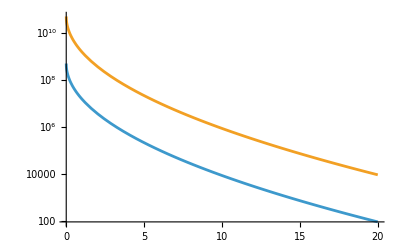

```mathematica
mu0 = 0;
sigmaE = Sqrt[6.];
barz0 = Exp[-mu0 + sigmaE^2/2];
barz[x_]:=barz0*Exp[sigmaE*Sqrt[2*x]]

LogPlot[{10^10/barz[x], 10^12/barz[x]}, {x, 0, 20}]
```

```mathematica
(16-3.5)^2/7.5/2
(16-2.5)^2/7.5/2
Log10[Exp[(16-3.5)^2/7.5/2]]
Log10[Exp[(16-2.5)^2/7.5/2]]
```

10.4167

12.15

4.5239

5.27668